## Applications

Is there a way for me to directly apply these methods to concrete computations? 
I could search for systems that represent chemical reactions directly, either by explicitly building in some/all rules related to forming bonds and/or by searching with genetic algorithms to find systems which approximate forms of chemistry. It seems that hypergraph (or simple graph) structures could be used to directly represent molecules - for example, by representing individual atoms by a number of self loops based on the number of valence electrons, and forming compounds by building bonding rules between them.

```mathematica
atom[n_]:=Graph[Table[{1,1}, n]]
```

```mathematica
h=atom[1];
o=atom[2];
```

```mathematica
rule = {{1,1},{ 2,2}}->{{1,2}};
```

```mathematica
init = {{1,1},{2,2},{2,2},{3,3}};
```

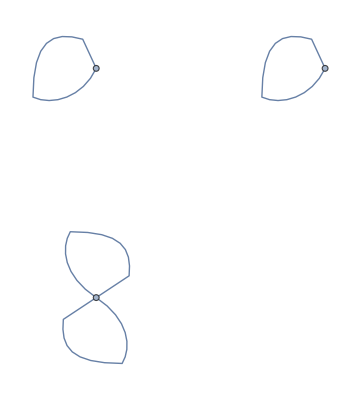
{-Graphics-,Graph[{{4},{5},{6},{7}}]}

```mathematica
Graph/@wm[rule, init, 1, "StatesList"]
```